Quantum Fourier Transform |

Definitionpaclet:Q3/tutorial/QuantumFourierTransform#1875748448 | Quantum Implementationpaclet:Q3/tutorial/QuantumFourierTransform#727891409
Physical Meaningpaclet:Q3/tutorial/QuantumFourierTransform#1970601676 | Semiclassical Implementationpaclet:Q3/tutorial/QuantumFourierTransform#1845626348

See also Section 4.3 of the Quantum Workbook (Springer, 2022)https://doi.org/10.1007/978-3-030-91214-7.

The quantum Fourier transform is a unitary transformation of quantum states. It is analogous to the discrete Fourier transform of a finite set of numbers. In the case of the quantum Fourier transform, the numbers are replaced with quantum states.

The quantum Fourier transform can be performed efficiently on a quantum computer consisting of n qubits with only O(n^2) elementary quantum gate operations, compared to O(n 2^n) gates for the best known classical algorithm for a discrete Fourier transform. This exponential speedup in the quantum Fourier transform algorithm relative to the classical counterpart enabled the celebrated quantum factorization algorithm to achieve a similar efficiency.

Apart from the above mentioned quantum factorization algorithm, the quantum Fourier transformation is a key part of many other quantum algorithms, such as the quantum phase estimation, the order-finding problem, the discrete logarithm, and most importantly the hidden subgroup problem. Such a wide range of applications of the quantum Fourier transform stems from the fact that all known quantum algorithms featuring an exponential speedup over classical algorithms are variations of the hidden subgroup problem and, as first realized by Kitaev (1996), the key step to solve the latter problem is the quantum Fourier transform.

Make sure that the Q3 package is loaded to use the demonstrations in this document.

```mathematica
<<Q3`
```

Throughout this document, symbol S will be used to denote qubits and Pauli operators on them. Similarly, symbol c will be used to denote complex-valued coefficients.

```mathematica
Let[Qubit,S]
Let[Complex,c]
```

## Definition

To make the physical meaning underlying the quantum Fourier transform clearer, in this document, we use a slightly different notation for the computational basis states, and denote them by

X_x:=x_1⊗x_2⊗⋯⊗x_n

for x=0,1,2,…,2^n-1, where x_k for k=1,2,…,n are the binary digits of x=(x_1 x_2(⋯x)_n)_2.

The quantum Fourier transform, QFT for short, is a unitary transformation defined by the association

U_QFT X_y:=1/2^(n/2)Σ_(x=0)^(2^n-1)X_x ⅇ^(ⅈ x p_y)

for y=0,1,2,…,2^n-1, where p_y is the y^th “wave number” defined by

p_y:=(2π y)/2^n=2(π(0. y_1 y_2(⋯y)_n))_2.

Like x_k, y_k for k=1,2,…,n are the binary digits of y=(y_1 y_2(⋯y)_n)_2.

The expression on the right-hand side of the above definition is of a familiar form of the discrete Fourier transform except that instead of numerical coefficients for the exponential factor ⅇ^(ⅈ x p_y), there appear state vectors. Therefore, one may think of the quantum Fourier transform as a vector-valued discrete Fourier transformation.

## Physical Meaning

In many physical applications, there is a more important aspect of the quantum Fourier transform than its formal similarity to the discrete Fourier transform. It is useful and inspiring to regard the QFT as a basis change, a unitary transformation from the computational basis

{X_x:x=0,1,2,…,2^n-1}

to the so-called “conjugate basis”

{P_y:=U_QFT X_y:y=0,1,2,…,2^n-1}.

The key observation is that in the “continuum” limit (L := 2^n→ ∞), the computational basis corresponds to the eigenbasis of the “position” and the conjugate basis to that of the “momentum”. Indeed, one can see that the two observables

X:=Σ_x X_xxX_x     and     P:=Σ_y P_y p_y P_y

bearing eigenvalues x and p_y, respectively, satisfy the relation

ⅇ^(-ⅈ a P)X ⅇ^(+ⅈ a P)=X - a I.

This implies that ⅇ^(-ⅈ a P)is a translation operator, and P is the generator of the translation, i.e., the momentum.

This notion can be made rigorous even in a finite-dimensional Hilbert space using the unitary operators exp(-ⅈ p X) and exp(-ⅈ a P), which generate the so-called Weyl-Heisenberg group;  see Weyl (1931, Section IV.14) for example.

The quantum Fourier transform appears frequently in many quantum algorithms (notably the quantum phase estimation algorithm), in an explicit or disguised form. The relation between the computational and conjugate basis defined above is useful to understand the principle behind the particular algorithms.

## Quantum Implementation

```mathematica
<<Q3`
```

```mathematica
Let[Qubit,S]
Let[Complex,c]
```

The quantum Fourier transform algorithm is to efficiently implement the unitary operator U_QFT in terms of the elementary gates. Getting back to the definition, the quantum Fourier transform maps the quantum states by

U_QFT X_y:=1/2^(n/2)Σ_(x=0)^(2^n-1)X_x ⅇ^(ⅈ x p_y)

with wave number

p_y:=(2π y)/2^n

for y=0,1,2,…,2^n-1.

Since the characteristic properties of the Fourier transform of any kind are attributed to an oscillatory phase factor ⅇ^(ⅈ x p_y), we start by elaborating it. The product x p_y in the exponent is given by

x p_y=(2π x y)/2^n=2(π(0. x_1 x_2(⋯x)_n))_2 y=2π yΣ_(k=1)^n x_k 2^-k,

which recasts the phase factor into the form

exp(ⅈ x p_y)=Π_(k=1)^n exp(2π ⅈ y x_k 2^-k).

We put it back in the defining expression of quantum Fourier transform and rewrite the sum over x with the sum over bit values x_k∈{0,1}, which lead to

U_QFT X_y=⊗_(k=1)^n Σ_(x_k=0,1)x_k ⅇ^(2π ⅈ x_k y/2^k).

For a fixed k, the ratio y/2^k is represented in the binary digits as

y/2^k=(y_1 y_2(⋯y)_(n-k).y_(n-k+1)(⋯y)_(n-1)y_n)_2.

The integer part does not affect the sum because ⅇ^(2π ⅈ m)=1 for any integer m, and only the fractional part (0. y_(n-k+1)(⋯y)_n)_2 does. Depriving the phase factors ⅇ^(ⅈ x_k p_y) of the integer parts, we arrive at the expression for the result of the transformation

U_QFT X_y=⊗_(k=1)^n Σ_(x_k=0,1)x_k ⅇ^(2π ⅈ (x_k(0. y_(n-k+1)(⋯y)_(n-1)y_n))_2).

Explicitly writing the sums over bit values x_k, it reads as

U_QFT X_y=((0+1 ⅇ^(2π ⅈ 0. y_n))/(√2))⊗((0+1 ⅇ^(2π ⅈ 0. y_(n-1)y_n))/(√2))⊗⋯⊗((0+1 ⅇ^(2π ⅈ 0. y_1 y_2(⋯y)_n))/(√2)).

Interestingly, the state resulting from the quantum Fourier transform is clearly a product state. The first factor is stored in the first qubit of the quantum register, and consecutive factors are stored in the corresponding qubits in the same order. For later analysis, it is useful to reverse the order. This is equivalent to performing the qubit-reversing unitary transformation

U_QBR y_1⊗y_2⊗⋯⊗y_n=y_n⊗⋯⊗y_2⊗y_1 .

Applying first the qubit-reversing transformation before the quantum Fourier transform, we arrive at the final expression that we analyze subsequently

U_QFT U_QBR X_y=((0+1 ⅇ^(2π ⅈ 0. y_1))/(√2))⊗((0+1 ⅇ^(2π ⅈ 0. y_2 y_1))/(√2))⊗⋯⊗((0+1 ⅇ^(2π ⅈ 0. y_n(⋯y)_2 y_1))/(√2)).

So far, we have done nothing but re-express the defining equation of the quantum Fourier transform. Now, we identify the elementary quantum logic gates that compose the transform. The product in the above is particularly useful to analyze. Let us examine the state stored on the k^thqubit,

(0+1 ⅇ^(2π (ⅈ(0. y_k(⋯y)_2 y_1))_2))/(√2).

Noting that

2(π(0. y_k(⋯y)_2 y_1))_2=Σ_(j=1)^k y_j 2^(j-k)π,

we see that qubits 1,2,…,k makes relative phase shifts 2^(1-k)π, 2^(2-k)π, …, π, respectively. Among these, the phase shift π depends on the state y_k of the k^th qubit itself, and it is equivalent to the Hadamard gate. Therefore, we can regard that the above state stored on the k^th qubit is a result of the transformation

y_1⊗y_2⊗⋯⊗y_(k-1)⊗y_k↦y_1⊗y_2⊗⋯⊗y_(k-1)⊗(Π_(j=1)^(k-1)T^y_j(2^(j-k)π)Hy_k) ,

where T(ϕ) denotes the relative phase shift

T(ϕ)=00+11 ⅇ^(ⅈ ϕ)≐(1 | 0
0 | ⅇ^(ⅈ ϕ)) .

The actual operation of T^y_j(2^(j-k)π) is determined by the basis state y_j of the j^th qubit, so it is a controlled-unitary gate. For example, the state stored on the third qubit is represented in the quantum circuit as

```mathematica
PhaseQFT[k_Integer]:=Prepend[
Reverse@Table[
ControlledGate[S[j],S[k,C[j-k-1]],"Label"->Subscript["T",k-j]],
{j,k-1}],
S[k,6]
]
```

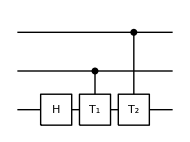

```mathematica
QuantumCircuit@@PhaseQFT[3]
```

where we have used the short-hand notation T_l:=T(π/2^l).

Overall, the quantum Fourier transformation can be represented in the quantum circuit as

```mathematica
QBR[n_Integer]:=Table[SWAP[S[j],S[n-j+1]],{j,n/2}]
```

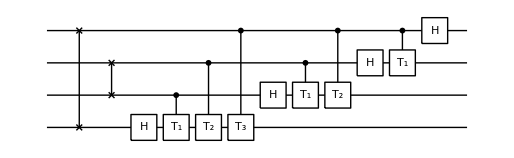

```mathematica
qc=QuantumCircuit[
Sequence@@QBR[4],
Sequence@@PhaseQFT[4],
Sequence@@PhaseQFT[3],
Sequence@@PhaseQFT[2],
S[1,6]]
```

where we have implemented the qubit-reversing transformation U_QBR by applying SWAP gates on pairs of qubits from the first and second half of the quantum register.

Check that the above quantum circuit indeed gives the quantum Fourier transform.

```mathematica
Matrix[qc]-FourierMatrix[2^4]//Simplify//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

### Conventional Form

In the above quantum circuit, we have applied U_QBR at the beginning. One can apply it at the end as well. Since U_QBR corresponds to a simple reversal of the order of qubits, the above quantum circuit is identical to the following quantum circuit

```mathematica
ReversedPhaseQFT[n_Integer,k_Integer]:=Prepend[
Table[
ControlledGate[S[j],S[k,C[k-j-1]],"Label"->Subscript["T",j-k]],
{j,k+1,n}],
S[k,6]
]
```

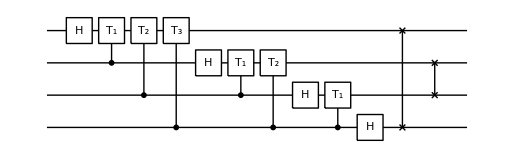

```mathematica
new=QuantumCircuit[
Sequence@@ReversedPhaseQFT[4,1],
Sequence@@ReversedPhaseQFT[4,2],
Sequence@@ReversedPhaseQFT[4,3],
S[4,6],Sequence@@QBR[4]]
```

```mathematica
Matrix[qc]-Matrix[new]//N//Chop//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

This quantum circuit for the quantum Fourier transformation is found more commonly in the literature.

### Computational Complexity

From the quantum circuits discussed above, we see that quantum Fourier transform requires an order of n^2 elementary gates. For example, consider again the quantum circuit

```mathematica
qc=QuantumCircuit[
Sequence@@QBR[4],
Sequence@@PhaseQFT[4],
Sequence@@PhaseQFT[3],
Sequence@@PhaseQFT[2],
S[1,6]]
```

-Graphics-

There are n Hadamard gates, one for each qubit. The number of controlled-unitary gates is given by ∑_(k=1)^n (k-1)=n(n-1)/2. There are n/2 SWAP gates as well, each of which requires three CNOT gates. Overall, we need n(n+4)/2 ∼ O(n^2) gates. This computational load is compared to O(n 2^n) gates for the fast Fourier transform (FFT), the best classical algorithm for the discrete Fourier transform.

## Semiclassical Implementation

```mathematica
<<Q3`
```

```mathematica
Let[Qubit,S]
Let[Complex,c]
```

The semiclassical implementation is not only interesting from a physical point of view, but it is also extremely interesting given the current level of technology (Griffiths & Niu, 1996). Since it does not require any entanglement, a quantum information resource that is the most fragile and hence difficult to maintain, many experiments are using this implementation whenever the QFT and/or the quantum phase estimation is in need (Chiaverini, 2005; Higgins et al., 2007).

The line of argument in the original work (Griffiths & Niu, 1996) to derive the semiclassical implementation of the quantum Fourier transformation is interesting in its own right, and it offers another physically-motivated derivation of the quantum Fourier transform algorithm. Here, Instead, we simply make use of the relation between the quantum Fourier transform and its inverse.

The inverse quantum Fourier transform is given by

U_QFT^†X_y=1/2^(n/2)∑_x X_x ⅇ^(-ⅈ x p_y),

which follows directly from the orthogonality relation

1/2^n∑_y ⅇ^(ⅈ(x-x')p_y)=δ_xx'.

The expression for the inverse quantum Fourier transform suggests that the inverse quantum Fourier transform is just another form of the quantum Fourier transform, and indeed, this is a characteristic property common to any kind of Fourier transform. This implies that one can recover the original quantum Fourier transform from the inverse quantum Fourier transform, and vice versa, in several ways.

For example, note that  U_QFT^†X_y is an element of the conjugate basis because

ⅇ^(-ⅈ x p_y)=ⅇ^(ⅈ x (2π-p_y))

for any x and y. In fact, U_QFT^†X_y=P_(2^n-y). More useful in the context of the semiclassical implementation of the quantum Fourier transform is to note that the inverse quantum Fourier transform U_QFT^† is nothing but the quantum Fourier transform with the phase factor ⅇ^(ⅈ x p_y) replaced by ⅇ^(-ⅈ x p_y). It corresponds to replacing the relative phase shifts T(ϕ) in the above quantum implementation by T^†(ϕ). Conversely, suppose that we start with the quantum circuit

```mathematica
qc=QuantumCircuit[Sequence@@QBR[4],
Sequence@@PhaseQFT[4],Sequence@@PhaseQFT[3],Sequence@@PhaseQFT[2],
S[1,6]]
```

-Graphics-

Take its Hermitian conjugate (i.e., inverse), and replace T^†(ϕ)≡T(-ϕ) with T(ϕ), then we should recover the original quantum Fourier transform. Through this procedure, we get the following quantum circuit for the quantum Fourier transform.

```mathematica
PhaseSQFT[k_]:=Append[
Table[ControlledGate[S[j],S[k,C[j-k-1]],"Label"->Subscript["T",k-j]],{j,k-1}],
S[k,6]]
```

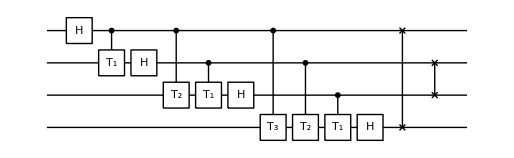

```mathematica
new=QuantumCircuit[S[1,6],
Sequence@@PhaseSQFT[2],
Sequence@@PhaseSQFT[3],
Sequence@@PhaseSQFT[4],
Sequence@@QBR[4]]
```

Compared to the previous quantum circuit, qc, the above quantum circuit has its Hadamard gate on a fixed qubit coming before the qubit “controls” the operation of the relative phase shift T(ϕ) on other qubits. This difference brings a significant consequence. To see it, we put explicit measurements on the qubits,

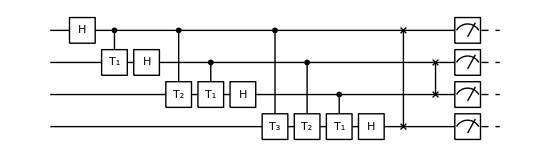

```mathematica
new=QuantumCircuit[S[1,6],
Sequence@@PhaseSQFT[2],
Sequence@@PhaseSQFT[3],
Sequence@@PhaseSQFT[4],
Sequence@@QBR[4],
Measurement[S[{1,2,3,4},3]]]
```

According to the principle of deferred measurement, the measurement can be performed before the controlled unitary gates

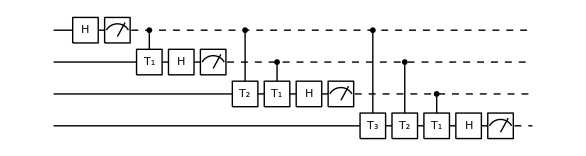

```mathematica
sqc=QuantumCircuit[S[1,6],Measurement[S[1,3]],
Sequence@@PhaseSQFT[2],Measurement[S[2,3]],
Sequence@@PhaseSQFT[3],Measurement[S[3,3]],
Sequence@@PhaseSQFT[4],Measurement[S[4,3]]]
```

This form is exactly the quantum circuit derived in Griffiths & Niu (1996). The important point is that after the measurement, the controlled-unitary gates become just classical feedback controls that require no entanglement.

| Related Guides
▪Quantum Information Systems
▪Q3

| Related Tech Notes
▪Quantum Fourier Transform: Semiclassical Implementation
▪Quantum Phase Estimation
▪Quantum Algorithms
▪QuantumCircuit Usage Examples
▪Quantum Information Systems with Q3
▪Quick Quantum Computing with Q3

| Related Links
▪A. Y. Kitaev, Electronic Colloquium on Computational Complexity 3, 3 (1996)http://arxiv.org/abs/quant-ph/9511026, “Quantum Measurements and the Abelian Stabilizer Problem.”
▪R. B. Griffiths and C.-S. Niu, Physical Review Letters 76 (17), 3228 (1996)https://doi.org/10.1103/physrevlett.76.3228, “Semiclassical Fourier Transform for Quantum Computation.”
▪J. Chiaverini https://doi.org/10.1126%2Fscience.1110335et al., Science 308 (5724), 997 (2005)https://doi.org/10.1126%2Fscience.1110335, “Implementation of the Semiclassical Quantum Fourier Transform in a Scalable System.”
▪B. L. Higgins, D. W. Berry, S. D. Bartlett, H. M. Wiseman, & G. J. Pryde, Nature 450 (7168), 393 (2007)https://doi.org/10.1038/nature06257, “Entanglement-free Heisenberg-limited phase estimation.”
▪Hermann Weyl (1931)https://www.google.com/books/edition/_/jQbEcDDqGb8C?hl=en, The theory of groups and quantum mechanics (Dover, 1931).
▪M. Nielsen and I. L. Chuang (2022)https://doi.org/10.1017/CBO9780511976667, Quantum Computation and Quantum Information (Cambridge University Press, 2011).
▪Mahn-Soo Choi (2022)https://doi.org/10.1007/978-3-030-91214-7, A Quantum Computation Workbook (Springer, 2022).